# EQLab package quick guide.

## Useful Info

1) Some definitions:

1.1) USER         →    one of us, someone who runs this package.

1.2) predictor → an expert, a person whose behaviour/belief we try to model

1.3) question  →  a  basic  ‘unit’ in an experiment, indexed by ‘i’.  Asking a question (fixed i) is  step that involves producing:
	a) forecasts  p_ij for each predictor ( for all values of   j )
	b) a measurement m_i (like tossing a die)
	c) resolutions v_ij for each predictor  ( for all values of   j ) 
	d) outcome q_i ( this reflects the resolution of the majority of predictors  )
	e) surprisals s_ij for each predictor  ( for all values of   j ) 
	f)  rewards r_ij  for each predictor  ( for all values of   j )  
	A question is stored in EQLab as a List :  question_i={p_i,m_i,v_i,q,s_i,r_i};  Where bold letters are each a List
	
1.4) Experiment → a set of questions asked in sequence (stored as a List of questions)

2)Some variable definitions:

2.1) npredictors →  number of  predictors  (cannot be modified after loading EQLab )
         nquestions →  number of  questions for each experiment (can be modified in between experiments)

2.2) npredictorsUSER →   number of  predictors, to be defined by user before  loading EQLab. (have no effect after loading)

## Steps to prepare simulations

Set user parameter values

```mathematica
npredictorsUSER=2;
```

Load package

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

Define functions needed for experiment. Needs the follow the prototypes below:

UserPredict[exp_ , newquestion_]       →  Function should return a List of numbers (forecasts) of size ‘npredictors’ ;    ‘exp’  and ‘newquestion’  are  as defined in EQLab  it is useful if predictors update their forecast based on previous questions and/or current measurement .

TR - set random number seed to try to compare with what i had before

```mathematica
SeedRandom[104]
```

RandomGeneratorState[…]

```mathematica
(*set initial forecast*)
setforecastinit[]:=(forecastinit=Table[Random[],{i,1,npredictors}];);
```

TR - changed these to match my dice game.

```mathematica
theoryforecasts={1/3,5/6};
(*random numbers M to model how each predictor 'reacts' for previous measurements*)
(*smaller M means more reactive*)
setreactioninit[]:=(reactivity=Table[RandomInteger[{1,20}],{i,1,npredictors}];)
(* reactivity={1,100,1,100}; *)
(*The prior probability for alpha theory for each player*)
priors = {99/100,1/100}
(* likelihoods for theories a and b. *)
likelihood = {theoryforecasts[[2]]/theoryforecasts[[1]],theoryforecasts[[1]]/theoryforecasts[[2]]} 
(*The initial forecasts for each player.*)
forecastinit={theoryforecasts[[1]]priors[[1]]+ theoryforecasts[[2]](1 - priors[[1]]),theoryforecasts[[1]]priors[[2]]+ theoryforecasts[[2]](1 - priors[[2]])} //N
```

{99/100,1/100}

{5/2,2/5}

{0.338333,0.828333}

```mathematica
pr =( theoryforecasts[[2]]-forecastinit[[1]])/(theoryforecasts[[2]]-theoryforecasts[[1]])
```

0.99

TR - Updated prediction module to not have the forecasts modified

```mathematica
(* pra = prior for theory A, prb = prior for theory B. poa and pob are the posteriors. *)
```

```mathematica
UserPredict[exp_,newquestion_]:=Module[
{THEORYFORC = theoryforecasts,LIKELIHOOD = likelihood,pra,prb,poa,pob,ipredictor,n=(exp//Length),ρnew,ρ,m,RHOnew={}},


For[ipredictor=1,ipredictor≤npredictors,ipredictor++,
If[n==0,
ρnew=forecastinit[[ipredictor]],
(* The prediction from the previous experiment: *)
ρ=exp[[n,1,ipredictor]];
(* The measurement: *)
m=exp[[n,2]];
(* The priors for alpha and beta. Get pra by inverting the expression for ρnew*)
pra=( THEORYFORC[[2]]-ρ)/(THEORYFORC[[2]]-THEORYFORC[[1]]); 
prb = 1 - pra; 
(*The posteriors.*)
poa = Which[m == 1,pra/(LIKELIHOOD[[1]](1-pra) +pra),m==-1,pra/(LIKELIHOOD[[2]](1-pra) +pra)];
pob = 1 - poa;
ρnew= THEORYFORC[[1]]*poa + THEORYFORC[[2]]*pob;
];
AppendTo[RHOnew,ρnew];];
RHOnew]
```

UserMeasure[] 	      →    Function should return either    +1 or -1.  (yes or no, like the toss of a die.)

TR - Changed prob to 1/3

```mathematica
prob=1/3;
UserMeasure[]:=(Random[]//Which[#<prob,1,True,-1]&);
```

UserResolve[exp_ , newquestion_]  	      →    Function should use the List  ‘newquestion[[2]]’ ( forecasts), and  return a List of numbers (resolutions) of the same size.  Arguments are   an experiment  and a question  as defined in EQLab. The variable ‘exp’ is useful only when modeling predictors that use knowledge from previous  questions in the experiment. Even If ‘exp’ is not used, the function must adhere to the  prototype.

```mathematica
UserResolve[experiment_,question_]:=UserResolve[question];
UserResolve[question_]:=Table[Random[]//Which[#<-0.5,-question[[2]],True,question[[2]]]&,{i,1,question[[1]]//Length}]
```

## Perform Experiments

#### Results of experiments are stored in the List called ‘EXPERIMENT’

```mathematica
EXPERIMENT
```

{}

#### By default, EQLab loads some predefined functions, So you can run an experiment.

TR - Default number of experiments is 20

```mathematica
RunExperiment[]
```

#### Now EXPERIMENT has one element (one experiment)

```mathematica
EXPERIMENT//Length
```

1

#### One can run another experiment, and check the size of EXPERIMENT again

```mathematica
RunExperiment[]
EXPERIMENT//Length
```

2

#### See contents of experiment 1

```mathematica
EXPERIMENT[[1]]//MatrixForm
```

({0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | 1 | {1,1} | 1 | {0.391705,1.74295} | {1.55848,0.267393}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | -1 | {-1,1} | 0 | {0,0} | {0,0}
{0.675904,0.175003} | -1 | {-1,-1} | -1 | {1.12671,0.192375} | {0.127847,0.745144}
{0.675904,0.175003} | -1 | {1,-1} | 0 | {0,0} | {0,0})

#### Use ShowPlots[] to see results for the lastest experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

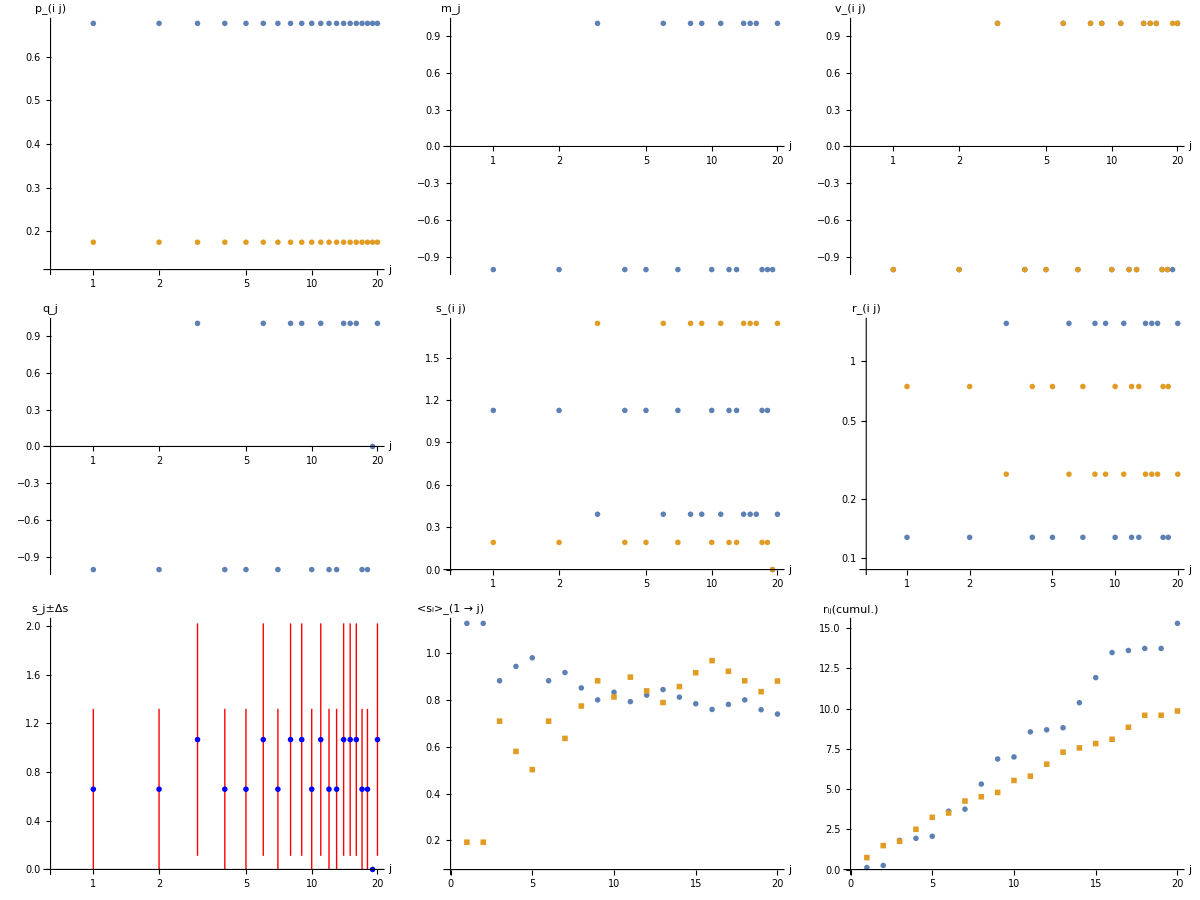

```mathematica
ShowPlots[]
```

#### Use ShowPlots[i] to see results for the ith experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

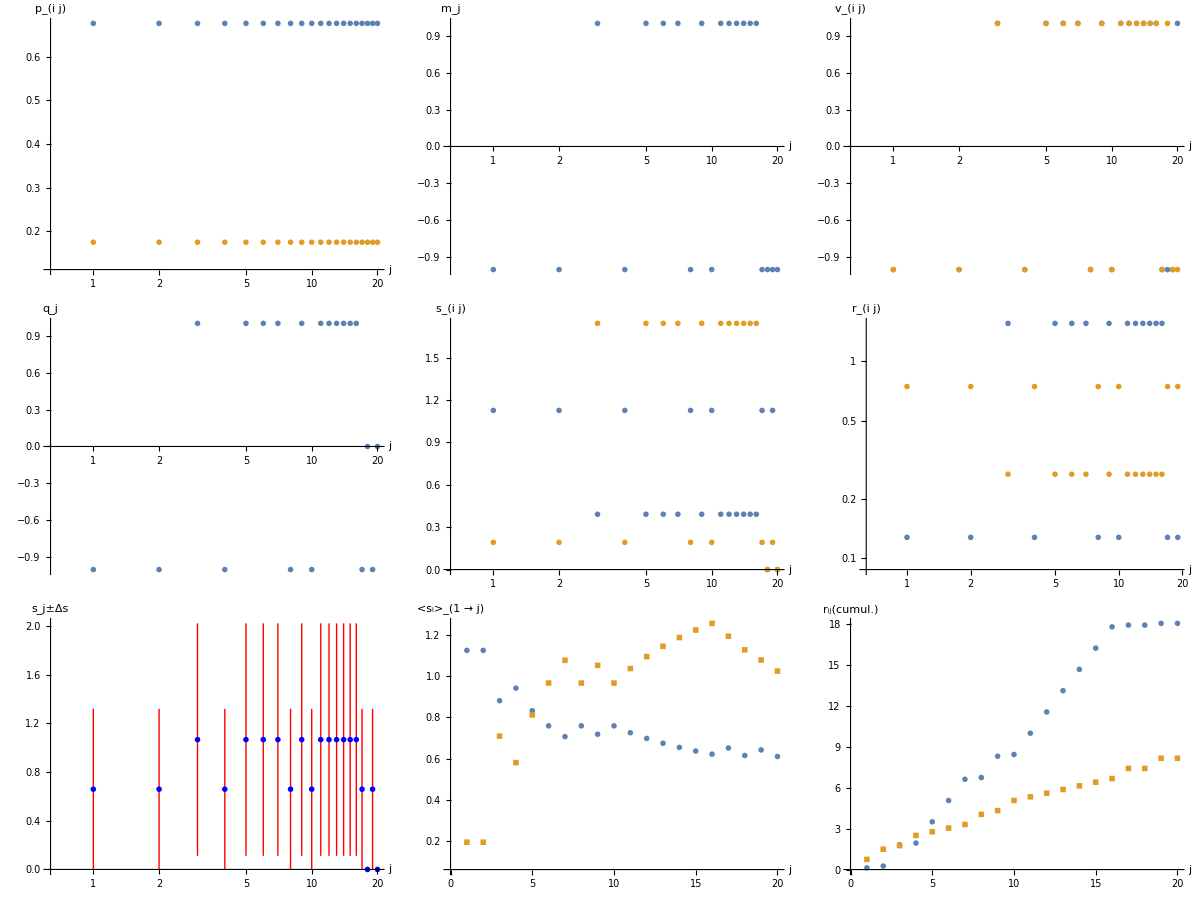

```mathematica
ShowPlots[1]
```

#### Experiments 1 and 2 where done with default functions and default values for ‘nquestions’. To use the custom functions defined above, one needs to load them with ‘SetUserFunctions[]’

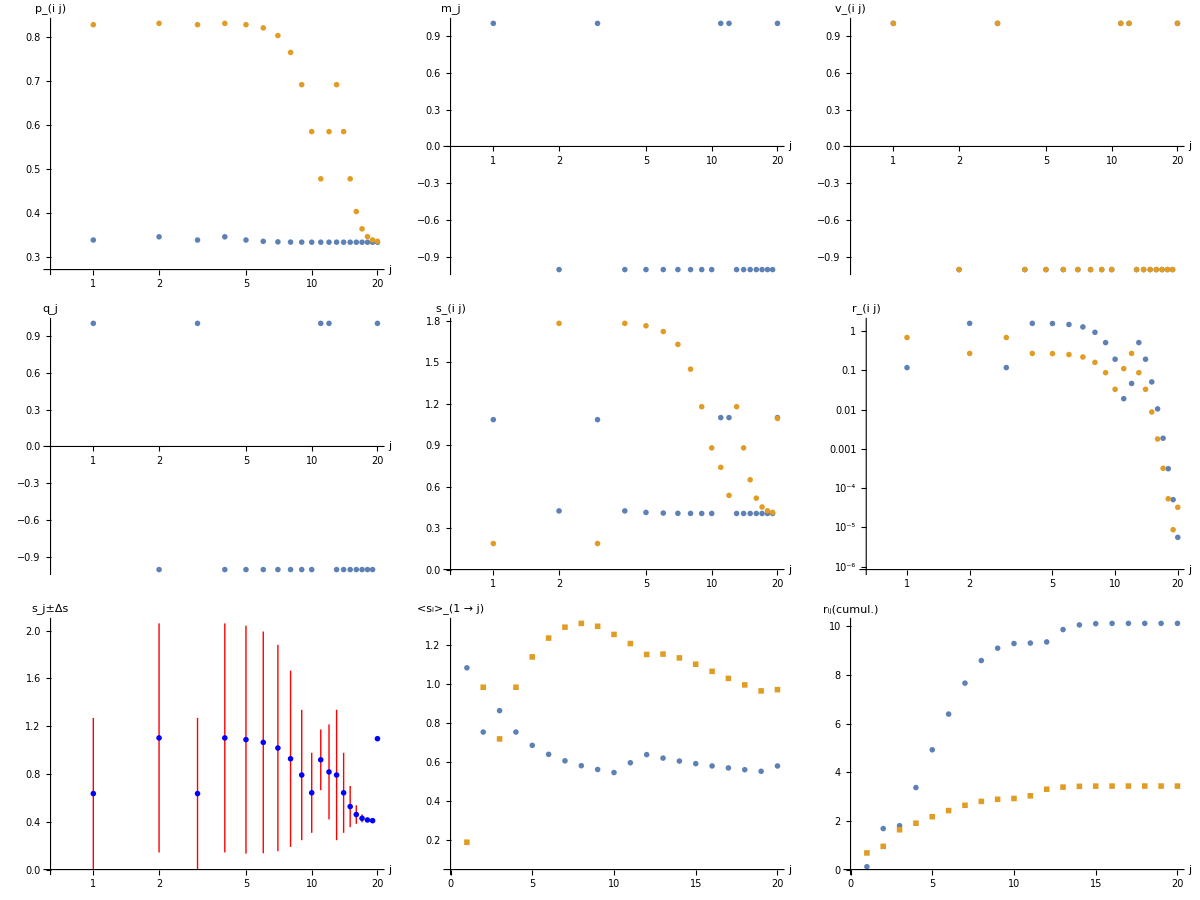

```mathematica
SetUserFunctions[]
RunExperiment[]
ShowPlots[]
```

#### ‘qpredictors’ and ‘nquestions’ can be reinitialized before running another experiment.

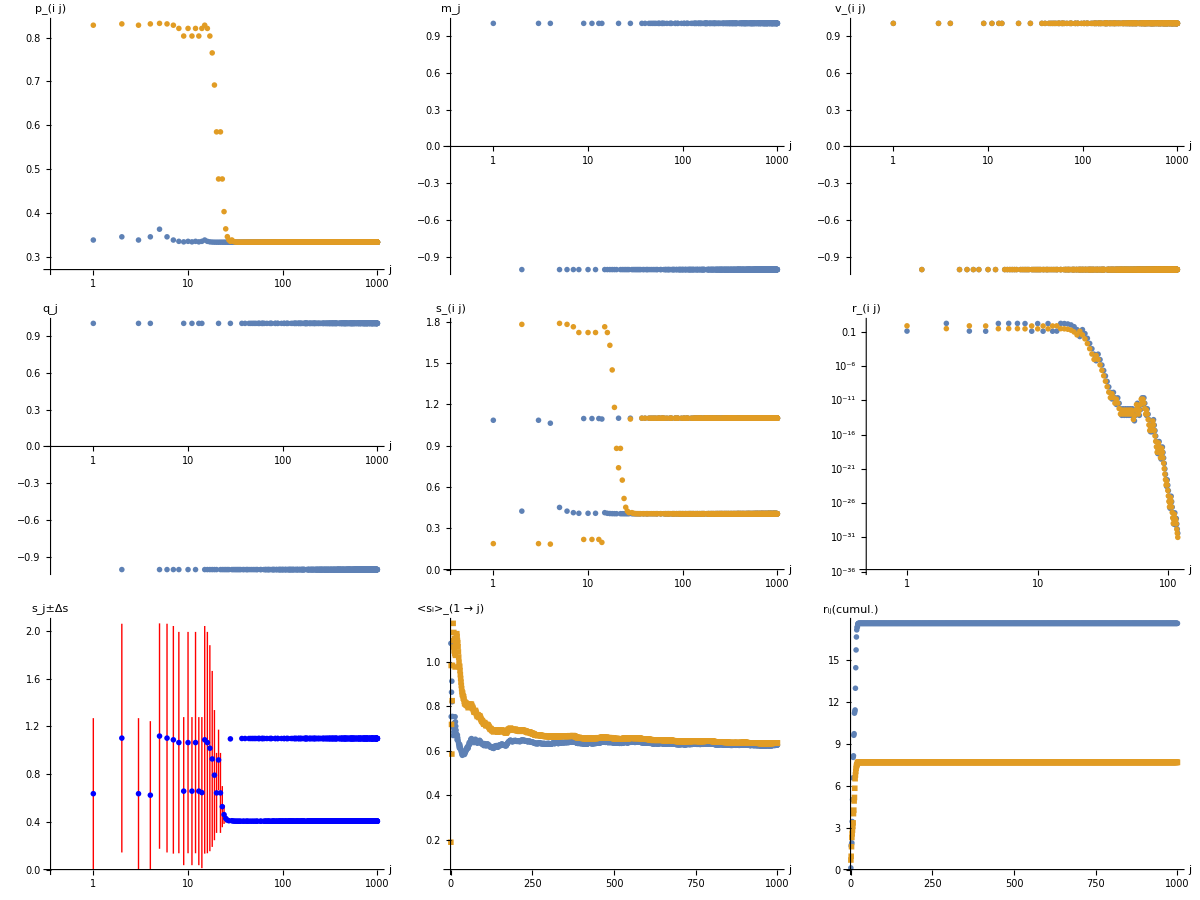

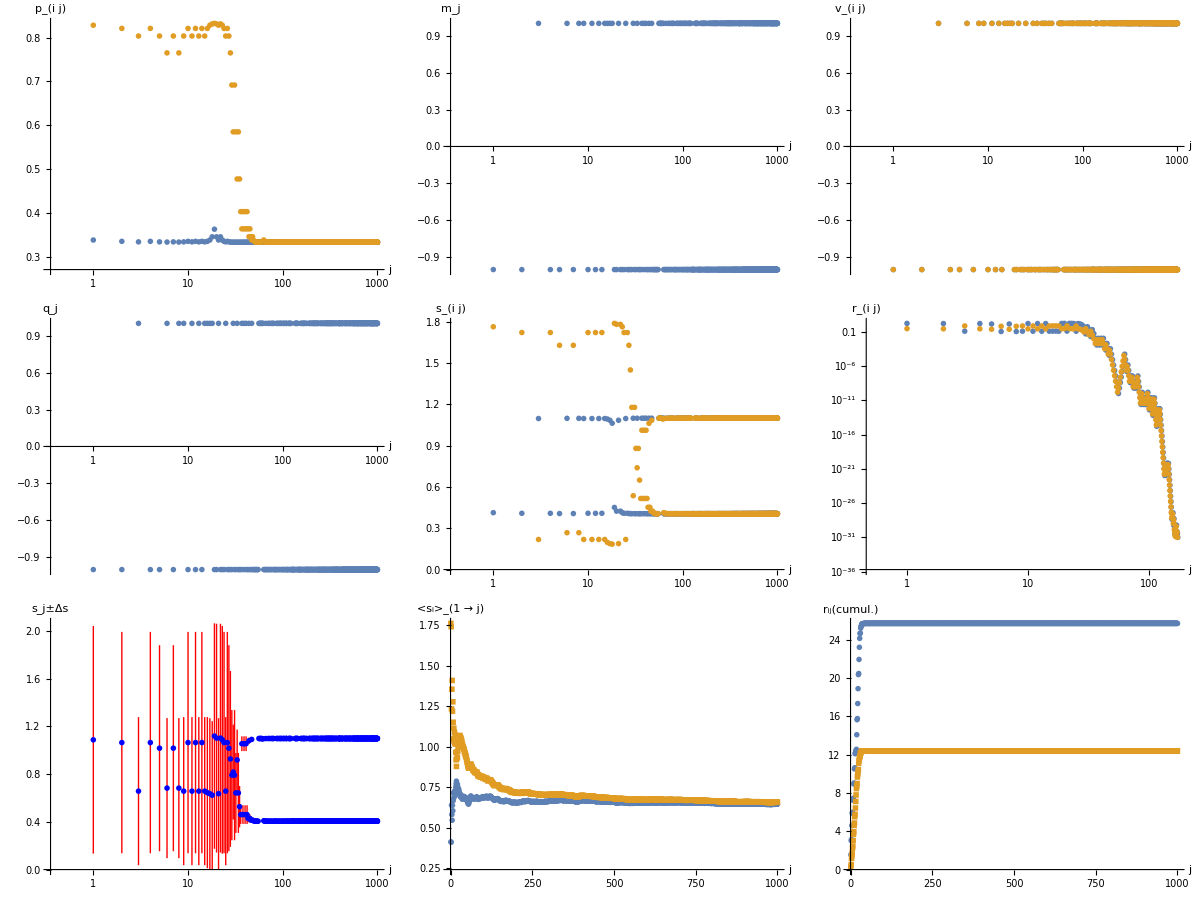

```mathematica
nquestions=1000;
RunExperiment[]
ShowPlots[]

npredictors=2;
RunExperiment[]
ShowPlots[]
```

#### work in progress: cumulative rewards (here for last experiment, with user functions)

```mathematica
Cumulative[array_]:=Module[
{i,output={array[[1]]},size=array//Length,c},

For[i=2,i≤ size,i++,
c=array[[i]]+output[[i-1]];
AppendTo[output,c];

];
output//N
]
r1=EXPERIMENT[[4,All,6]][[All,1]]//Cumulative;
r2=EXPERIMENT[[4,All,6]][[All,2]]//Cumulative;r3=EXPERIMENT[[4,All,6]][[All,3]]//Cumulative;r4=EXPERIMENT[[4,All,6]][[All,4]]//Cumulative;
r5=EXPERIMENT[[4,All,6]][[All,5]]//Cumulative;
ListPlot[{r1,r2,r3,r4,r5}]
```

Part::partw: Part 3 of {0.117408,0.684305} does not exist.

Part::partw: Part 4 of {0.117408,0.684305} does not exist.

Part::partw: Part 5 of {0.117408,0.684305} does not exist.

ListPlot::lpn: {{{1.,0.117408},{2.,1.68605},{3.,1.80346},{4.,1.91625},{5.,3.43954},{6.,5.00819},{7.,6.56196},{8.,8.03118},{9.,8.14397},{10.,9.61319},«990»},{{1.,0.684305},{2.,0.953442},{3.,1.63775},{4.,2.29513},{5.,2.55648},{6.,2.82562},{7.,3.09221},{8.,3.34428},{9.,4.00167},{10.,4.25374},«990»},{},{},{}} is not a list of numbers or pairs of numbers.

ListPlot[{1}]
 |  |  |  |

```mathematica
EXPERIMENT//Length
```

5

```mathematica
RunExperiment[]
```

```mathematica
MakePlots[]
```

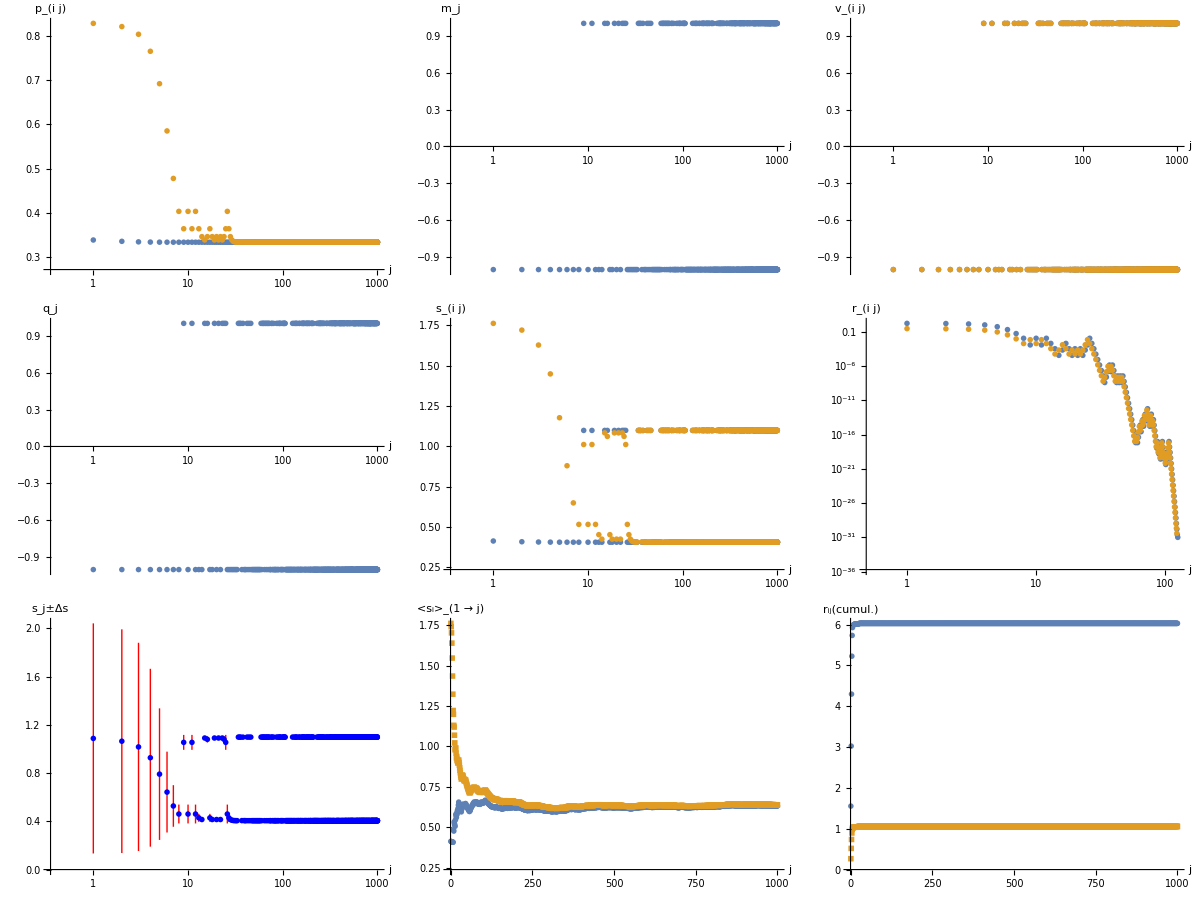

```mathematica
ShowPlots[]
```

```mathematica
npredictorsUSER=4;
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

```mathematica
For[i=1,i≤4,i++,RunExperiment[]];
```